# STROŠKI OLIMPIJSKIH IGER

Pridobivanje podatkov

```mathematica
ResourceSearch["Olympic Games"]
```

{ResourceObject[…]}

Shranimo podatke:

```mathematica
vsiPodatki = ResourceData["Olympic Games Costs"]
```

Dataset[<>]

Tiste Olimpijske Igre, za katere ni bilo podatkov o stroških, sem izbrisal iz tabele.

```mathematica
podatki = Delete[vsiPodatki, {{1}, {3}, {8}, {16}, {22}}]
```

Dataset[<>]

```mathematica
poletneIgre = Select[podatki, #["Type"] ==  "Summer" &]
```

Dataset[<>]

Spodaj vidimo graf, ki predstavlja stroške na posameznih Olimpijskih Igrah. Pričakoval sem, da bodo stroški pri kasnejših Olimpijskih Igrah večji, vendar tukaj to ni res. Že, na primer,  leta 1976 so bili stroški večji kot leta 2016, in celo dvakrat večji kot leta 2004. Vidimo, da so bili stroški daleč najvišji leta 2012 v Londonu.

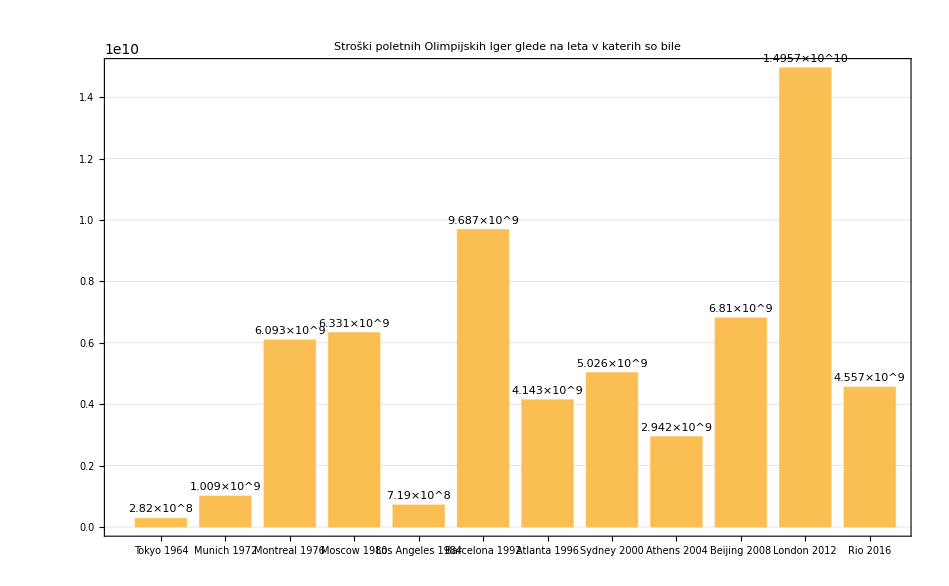

```mathematica
BarChart[poletneIgre[All, "Cost"], ChartLabels->{poletneIgre[All, "Games"]//Normal},LabelingFunction->Above, PlotLabel->"Stroški poletnih Olimpijskih Iger glede na leta v katerih so bile", ImageSize->Large, BarSpacing->Medium, PlotTheme->"Detailed"]
```

```mathematica
zimskeIgre = Select[podatki, #["Type"] ==  "Winter" &]
```

Dataset[<>]

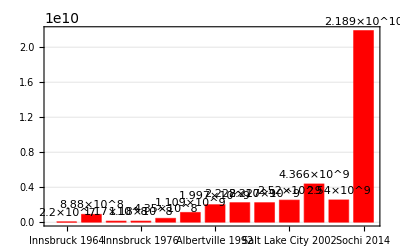

```mathematica
BarChart[zimskeIgre[All, "Cost"], ChartLabels->{zimskeIgre[All, "Games"]//Normal},LabelingFunction->Above, PlotLabel->"Stroški zimskih Olimpijskih Iger glede na leta v katerih so bile", ImageSize->Full, BarSpacing->Medium, PlotTheme->"Detailed", ChartStyle->{Red}]
```

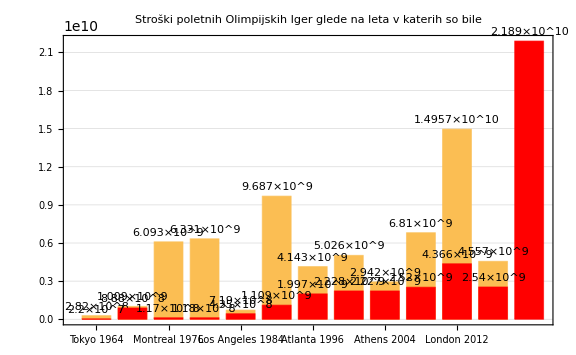

```mathematica
Show[g1, g2]
```

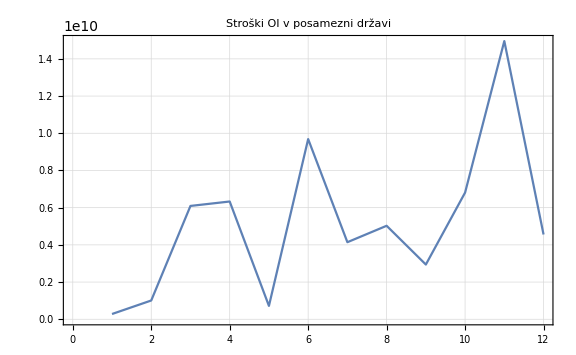

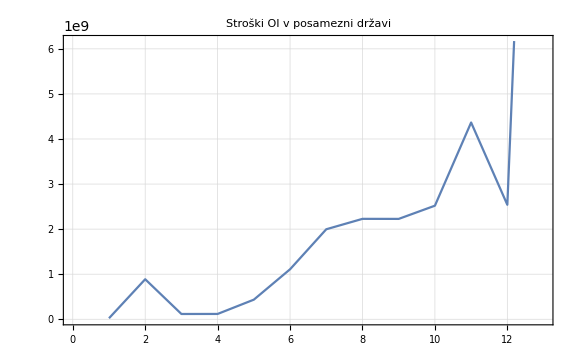

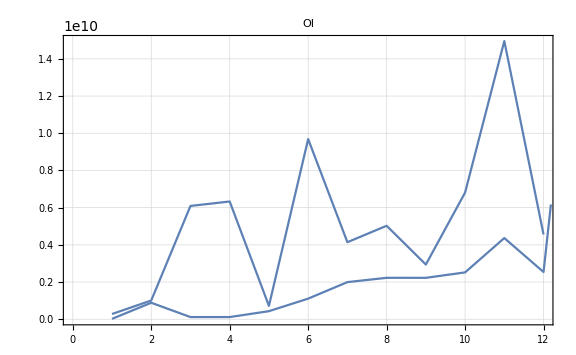

```mathematica
g1 = ListLinePlot[poletneIgre[All, "Cost"], PlotLabel->"Stroški OI v posamezni državi", PlotTheme->"FullAxesGrid", ImageSize->Large]
g2 =ListLinePlot[zimskeIgre[All, "Cost"], PlotLabel->"Stroški OI v posamezni državi", PlotTheme->"FullAxesGrid", ImageSize->Large]
Show[g1, g2, PlotLabel->"OI"]
```

```mathematica
Position[podatki,  "United States"]
```

{{5,Key[Country]},{7,Key[Country]},{17,Key[Country]},{22,Key[Country]}}

```mathematica
Length[podatki]
```

25

```mathematica
vsi = DeleteMissing[podatki[All, "Cost"]]
```

Dataset[<>]

```mathematica
Length[vsi]
```

25

```mathematica
DeleteMissing[podatki [All,{"Games","Cost"}]]
```

Dataset[<>]

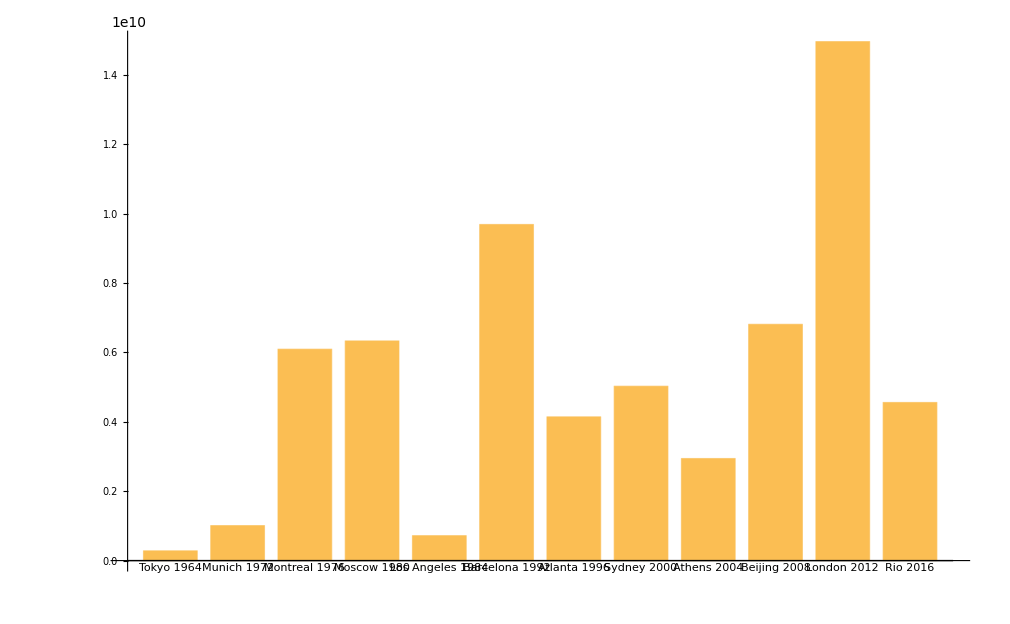

```mathematica
BarChart[dobriPodatki[All, "Cost"], ChartLabels-> {dobriPodatki[All, "Games"]//Normal}, ImageSize->Full, BarSpacing->Medium]
```

```mathematica
ListPlot[dobriPodatki["Cost"]]
```

ListPlot::lpn: … is not a list of numbers or pairs of numbers.

ListPlot[Failure[…]]

```mathematica
vrednosti = #["Country"]-> #["Cost"]& /@dobriPodatki
```

Dataset[<>]

```mathematica
ListPlot[vrednosti]
```

ListPlot::argx: ListPlot called with 0 arguments; 1 argument is expected.

ListPlot[{Japan→2.82e8 $,Germany→1.0089999999999999e9 $,Canada→6.093e9 $,Soviet Union→6.331e9 $,United States→7.19e8 $,Spain→9.687e9 $,United States→4.143e9 $,Australia→5.026e9 $,Greece→2.942e9 $,China→6.81e9 $,United Kingdom→1.4957e10 $,Brazil→4.557e9 $}]

```mathematica
Max[dobriPodatki["Cost"]]
```

Failure[…]

```mathematica
ListLinePlot[dobriPodatki[All, "Cost"], PlotLabel->"Stroški OI v posamezni državi", PlotTheme->"FullAxesGrid", ImageSize->Large]
```

-Graphics-

```mathematica
data=QuantityArray[EntityValue[EntityClass["Element",All],{"AtomicMass","MeltingPoint"}]]
```